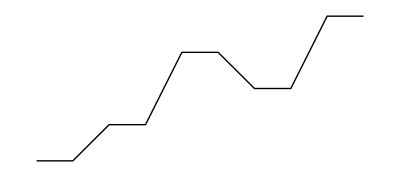

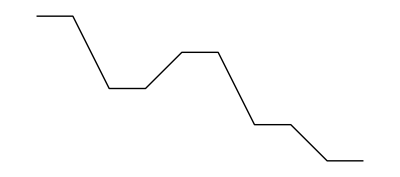

{1,2,3,4,5}

-Graphics-

{5,4,3,2,1}

```mathematica
seq = {1,2,3,4,5};     (* flow of a cord *)

cord[seq_]:= Block[      (* seq to line *)
	{ pos2, fn},
	seq2 = Riffle[seq, seq] ;   (* take every list item twice *)
	fn[y_,{x_}]:=  {x,y};       (* function to turn the result of MapIndexed into coordinates *)
	MapIndexed[fn, seq2]        (* wrapping coordiantes into a line *)
]

showCord[seq_]:= Graphics @ Line @ cord[seq] (* drawing cord *)
showBraid[seq_] := showCord /@ seq // Show

functionBraid[seq_, fn_, n_: 20] :=  (Transpose @ NestList[fn, seq, n])

cordFlip[seq_, crd_] :=  Block[
	{ 
		cord1 = crd, 
		cord2 = crd + 1 
	},
    seq /. {cord1 -> cord2, cord2 -> cord1}
]
MirrorVertically[seq_, max_]:= {
max-seq[[1]],max-seq[[2]], max-seq[[3]], max-seq[[4]], max-seq[[5]]
}
Show[ showCord[cordFlip[seq, 3]]]
Show[ showCord[cordFlip[Reverse[seq], 3]]] (*flipped on vertical axis*)
Show[ showCord[cordFlip[MirrorVertically[seq, 6], 3]]]
MirrorVertically[seq, 6]
```